```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
datrotuwsoca=Flatten[Import["trot_0.37_nutcalca.dat"]];
datrotdwsoca=Flatten[Import["trot_0.37_ndtcalca.dat"]];
datrotuwsocb=Flatten[Import["trot_0.37_nutcalcb.dat"]];
datrotdwsocb=Flatten[Import["trot_0.37_ndtcalcb.dat"]];
```

```mathematica
impdiffdata=Table[Partition[(datrotuwsoca+datrotdwsoca),3][[i,1]] + Partition[(datrotuwsoca+datrotdwsoca),3][[i,2]]+ Partition[(datrotuwsoca+datrotdwsoca),3][[i,3]],{i,1,Nx*Ny}]-4;

diffdata=impdiffdata;
```

```mathematica
impdiffdatb=Table[Partition[(datrotuwsocb+datrotdwsocb),3][[i,1]] + Partition[(datrotuwsocb+datrotdwsocb),3][[i,2]]+ Partition[(datrotuwsocb+datrotdwsocb),3][[i,3]],{i,1,Nx*Ny}]-4;

diffdatb=impdiffdatb;
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]]}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]]}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=-0.25;
fminval=-0.25;
maxval=Max[limval];

plalldiffdata=Table[If[alldiffdata[[i,3]]<=minval,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],fminval },pt = {alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]] }];pt,{i,1,Length[alldiffdata]}];
```

```mathematica
squarelength=4;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

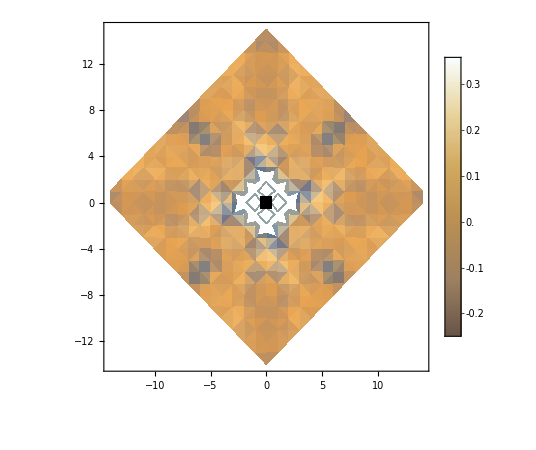

```mathematica
cntlegend=BarLegend[{"CoffeeTones" ,{fminval,maxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
graphicsplot=ListDensityPlot[plalldiffdata,(*ColorFunction -> (ColorData["CoffeeTones",(#)^(1) (*(1 - #)^e*)] &),
PlotRangeClipping -> False,Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},*)LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]},Epilog -> {Rotate[Text[Style["Site",35],{-18,1}],Pi/2],Text[Style[" Site",35],{0, -19}]},ImagePadding->{{58,80},{60,9}},ImageSize->450,AspectRatio->1];

fingraphicsplot=Legended[graphicsplot,Placed[cntlegend,{{0.88,0.78},{-0.48,0.86}}]];
impuritysite=Graphics[{Black,Rectangle[{-0.5,-0.5},{0.5,0.5}]}];
plwithimp=Show[fingraphicsplot,impuritysite]
Export["plwithimp.png",plwithimp];
Export["cntlegend.eps",cntlegend];
```